init

```mathematica
(*Import data*)
$FKKSRoot = NotebookDirectory[]<>"../";
$SolutionPath = $FKKSRoot<>"Solutions/";
<<SpinWeightedSpheroidalHarmonics`;
<<Teukolsky`;
NotebookEvaluate[NotebookDirectory[]<>"../Tests/NilsFunctions.nb"];
Import[NotebookDirectory[]<>"../Packages/HelperFunctions.wl"];
Import[NotebookDirectory[]<>"../Packages/KerrWithProca.wl"];
testsol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv31_100m1η0n0l0s-1χ9_10KMax4branch1.mx"];

TeukolskyTintegrandExpl=Import[NotebookDirectory[]<>"TeukolskyTintegrandExplRunNilsCode.mx"];

NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
```

```mathematica
tes$$[2] = Interpolation[{1,2,3,4,3,2,1}];
tes$$[3] = Interpolation[{2,3,4,5,6,5,4,3,2}];
out = <|"tes"->tes$$|>
```

<|tes→tes$$|>

```mathematica
DownValues[Evaluate@out["tes"]]
```

{HoldPattern[tes$$[2]]:>InterpolatingFunction[…],HoldPattern[tes$$[3]]:>InterpolatingFunction[…]}

```mathematica
nilsdat = NilsSolToMySol[#, 1,0,0.9,-1]&/@(Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/NilsSiemonsenCode/OG_Code_MyExecution/surrogate/m1n0_a900000_Sm1_prec_p_HPee.mx"]//Transpose);
mydat = getResults[$SolutionPath, {{"m",1},{"n",0}, {"μNv", "3_50"}}]//First;
nilssol = nilsdat[[6]];
```

ReplaceAll::reps: {0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction[…]

InterpolatingFunction[…]

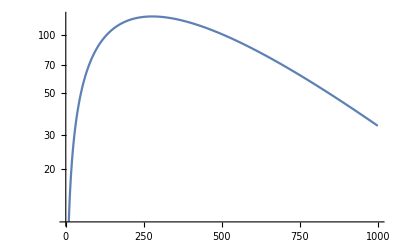

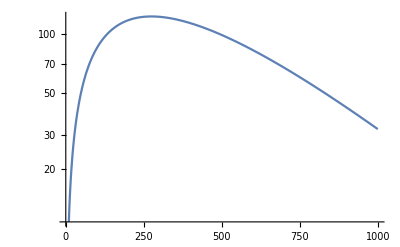

```mathematica
nilr =nilssol["Solution", "R"]
myr=RecastInterpolationFunction[mydat["Solution","R"], HorizonCoordToRadial[#,0.9]&]
LogPlot[nilr[r]//Abs, {r,1.436, 1000}]
LogPlot[myr[r]//Abs, {r,1.436, 1000}]
```

```mathematica
startingr = testsol["Parameters", "StartingX"];
endingr = testsol["Parameters", "EndingX"];
FrobeniusSystem[κ,c1,c2, testsol["Solution","ν"], testsol["Solution", "ω"], testsol["Parameters"]];
NSolve[%, {κ,c1,c2}, VerifySolutions->True, WorkingPrecision->testsol["Parameters"]["precision"]];
%[[1, All, 2]];
FrobeniusSeries[xN, Sequence@@%];
LogPlot[%//Abs, {xN, 0.0001, 1}]
LogPlot[testsol["Solution", "R"][r]//Abs, {r,0.0001,416}, PlotRange->All]
```

```mathematica
TruncateInterpolatingFunction[testsol["Solution", "R"], (#<250&), OnDomain->True]

LogPlot[%[r]//Abs, {r,0.0001,250}, PlotRange->All]
```

```mathematica
Block[{
	mv= testsol["Parameters", "m"],
	mTeu= 2*testsol["Parameters", "m"],
	nv = testsol["Parameters", "n"],
	spinin = testsol["Parameters", "χ"],

	χ1 = testsol["Parameters", "χ"],
	Mini = 1,
	μv = testsol["Parameters", "μNv"],
	ωrv = testsol["Solution", "ω"]//Re,
ωTeu = Re[2*testsol["Solution", "ω"]],
	ωiv = testsol["Solution", "ω"]//Im,
	νrv = testsol["Solution", "ν"]//Re,
	νiv = testsol["Solution", "ν"]//Im,
rstopcdoe = 621.36
},
 Do[
GenerateNilsMST[spinin,-2,j,l,2, 2*ωrv, rstop],
{l,{2,3,4}},{j,{2}}]

]
```

```mathematica
AllDat = Import/@FileNames[All, NotebookDirectory[]<>"../Solutions"];
```

```mathematica
$FKKSRoot  = "/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/"
Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/Packages/HelperFunctions.wl"]
Import[NotebookDirectory[]<>"../Packages/xActSetup.wl"];
Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/Packages/TeukolskySolver.wl"]
```

```mathematica
n0m1= OvertoneModeGroup[0,3,AllDat];
```

```mathematica
inx =n0m1[[All, "Parameters", "μNv"]]//Ordering;
Dat = n0m1[[inx]];
```

```mathematica
getResults[$SolutionPath, ]
```

```mathematica
Dat[[-3]]
```

```mathematica
s
```

```mathematica
N1
```

```mathematica
testsol = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/Solutions/FullSolutionSetRunData_ϵ1_10000μNv11_100m3η0n0l2s-1χ9_10KMax4branch1.mx"];
tnntest = Tnn[testsol, AsOptimized->True];
```

```mathematica
(mat = {{1,0,1},{0,1,1},{1/Sqrt[2], 1/Sqrt[2],1}});
(matinv = Inverse[mat]//Simplify);
mat//MatrixForm
matinv//MatrixForm
Reprrule = {N1->tnntest[0,r,θ,0], N2->tnntest[0,r,θ,π/(4*testsol["Parameters", "m"])], N3->tnntest[0,r,θ,π/(8*testsol["Parameters", "m"])]};
coefflist = matinv.{N1,N2,N3}//FullSimplify;
coeff1 = coefflist[[1]];
coeff2 = coefflist[[2]];
coeff3 = coefflist[[3]];
```

```mathematica
coeff11 = OptimizedFunction[{t,r,θ,ϕ}, Evaluate[coeff1/.Reprrule]];
```

```mathematica
coeff11[0,2,1,0]
```

```mathematica
solution = testsol;
Dmat[phi1_, phi2_, phi3_] := {{Cos[2*solution["Parameters", "m"]*phi1],Sin[2*solution["Parameters", "m"]*phi1],1},{Cos[2*solution["Parameters", "m"]*phi2],Sin[2*solution["Parameters", "m"]*phi2],1}, {Cos[2*solution["Parameters", "m"]*phi3],Sin[2*solution["Parameters", "m"]*phi3],1}}
```

```mathematica
ϕsampling = {0, π/(4*solution["Parameters", "m"]), π/(8*solution["Parameters", "m"])}
```

```mathematica
LinearSolve[Dmat[Sequence@@ϕsampling], {Aa,Bb,Cc}]//FullSimplify
```

```mathematica
tnnif = Tnn[testsol, AsInterpolatingFunction->True]
```

```mathematica
tnnif[4,100,2,5]/.r->100/.θ->2
tnntest[4,100,2,5]
```